# Linjär Algebra Projekt

## MA2027 Linjär Algebra VT19

Rapportversion 1, inlämnad 2019

## Team

André Frisk

Fredrik Kortetjärvi

Kristoffer Guachalla

Rohullah Khorami

William Wahlberg

## Problem 1 Vi vill simulera rörelsen för en satellit i bana kring jorden.

```mathematica
CurrentValue[EvaluationNotebook[],DefaultNaturalLanguage]="Swedish";
```

### A) Använd Newtons 2. lag och visa att satellitens acceleration vid en punkt med lägesvektor.

#### Lösning

F = (GMm)/(r^2)*e_r
a*m = (GMm)/(r^2)*e_r
a = (GM)/(r^2)*e_r
a = (GM)/(r^2)*e*r/(r^2)*r
a = -GM/(r^3)*r

### 1b/c) Vid tiden t = 0 befinner sig satelliten vid r0 = (1.5, 0) med hastigheten v0 = (0, 4.5). Bestäm ortsvektorn för satelliten som funktion av tiden genom iterering i små, men ändliga tidssteg ∆t rk+1 = rk + vk ∆t, vk+1 = vk + ak ∆t. (Använd ListPlot till att plotta banan)

Lösningar:
r_k+1 = r_k + v_k T
v_k+1 = v_k + a_k T
a = (-GM/r^3 )r 
v_k+1 = v_k + (-GM/r^3)r *T
r_k+1 = r_k + (v_k+(-GM/r^3)r *T )T

#### Lösning och svar med Mathematica koden

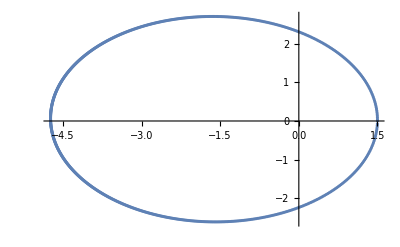

```mathematica
r = {1.5,0};
v = {0,4.5};


list = {};
i = 0;
varv = 773;
While[i<varv,
list = Append[list,r];
r += v*0.01;
v+= -20/(Norm[r])^3*r*0.01;

i++;
]

list;
ListPlot[list]
```

### D) Bestäm omloppstiden med två siffrors noggrannhet.

#### T = 7.66 timmer Lösning och svar med Mathematica

```mathematica
r = {1.5,0};
v = {0,4.5};


list = {};
i = 0;
varv = 773;
While[i<varv,
list = Append[list,r];
r += v*0.01;
v+= -20/(Norm[r])^3*r*0.01;

T = i *0.01;
ω = VectorAngle[r,{1.5,0}];
If[ω > 175.7 Degree,i= varv,i=i];
i++;
]
N[2*T]
```

7.4

### E) Sätt istället begynnelsehastigheten v0 = (0, 6.0). Vilken bana följer satelliten nu ? Ge en kvalitativ förklaring på vad som händer.

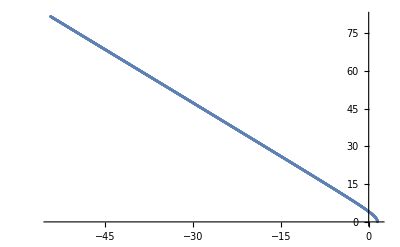

```mathematica
r = {1.5,0};
v = {0,6};

list = {};
For[i=0,i<3000,i++,
list = Append[list,r];
r += v*0.01;
v+= -20/(Norm[r])^3*r*0.01;
]
list;
ListPlot[list]
```

#### slutsats:

Då hastigheten är så pass hög åker satelliten utanför jordens gravitationsfält då jordens gravitationsfält inte kan upprätthålla en omloppsbana för satelliten p.g.a hastigheten. Därför kommer den åka i en linjär riktning ut i rymden som visas i grafen efter att grafen har passerat y-axeln. Det innan visar satellitens bana inom gravitationsfältet.

## Problem 2 En länkarm har massan m och tyngdpunkt/masscentrum i punkten G. Armen är fritt ledad i punkten O. I punkterna A, B respektive C finns inästningar för en fjäder och en lina som löper över en stationär trissa vid punkten D (försumma trissans dimensioner). Fjädern är i ospänd läge 2.0 m lång och ger en kraft F = k s p˚a armen, däres är förlängningen/kompressionen av fjädern. Om armen befinner sig i jämvikt måste summan av alla kraftmoment på armen vara noll. a) Identifiera alla krafter som ger ett moment (m.a.p. O) och uttryck både krafterna och ortsvektorer fökrafternas angrepspunkter på komponentform. Ledning: Skriv alla vektoriella storheter som ett belopp multiplicerad med en enhetsvektor

## Lösning:

Tyngdkraften = m* g
F_t
F_f= k * s

 G = (Sin(θ)*1.4,Cos(θ)*1.4)
 F_g_ = (0,-m*g)
 
 C = (Sin(θ)*4.2,Cos(θ)*4.2)
 F_c = (((1, 0).F_tx)/((1,0).(1,0))*(1,0)),((((0, 1).F_ty)/((0,1).(0,1)))*(0,1))
 
 B = (Sin(θ)*4.2,Cos(θ)*4.2)
 F_B = (((1, 0).F_fx)/((1,0).(1,0))*(1,0)),((((0, 1).F_fy)/((0,1).(0,1)))*(0,1))

B)  Ställ upp och lös (moment)jämviktsekvationen med avseende på beloppet av spännkraften i linan.
Uttryck denna som en funktion av vinkeln, dvs T(θ).

Svar som fick  från Mathematica

{T→(0.+37338. Sin[θ]-(70560. Sin[θ])/(√(Abs[4.2-4.2 Cos[θ]]^2+Abs[0.+4.2 Sin[θ]]^2)))/((19.6 Cos[θ])/(√(Abs[2.+2.8 Cos[θ]]^2+Abs[7.-2.8 Sin[θ]]^2))+(5.6 Sin[θ])/(√(Abs[2.+2.8 Cos[θ]]^2+Abs[7.-2.8 Sin[θ]]^2)))}

Lösning med Mathematica kod

```mathematica
ClearAll["Global`*"];

m = 150; "kg";
g = -9.8; "m*s^-2";
k = 2000; "N*m^-1";

OG = 1.4*{Sin[θ],-Cos[θ],0};
OC = 2.8*{Sin[θ],-Cos[θ],0};
OB = 4.2*{Sin[θ],-Cos[θ],0};
OA =  4.2*{0,-1,0};
d = {7,2,0}; 
AB = (OB - OA);
CD = d - OC;
f = k * (2.0 - Norm[AB]);
Subscript[AB, n]=Normalize[AB];
Subscript[CD, n]=Normalize[CD];

Subscript[F, T]= T * Subscript[CD, n];
Subscript[F, f]= f * Subscript[AB, n];
Subscript[F, G]= {0,m*g,0};

Subscript[M, g]= Cross[OG,Subscript[F, G]];
Subscript[M, T]= Cross[OC,Subscript[F, T]];
Subscript[M, f]= Cross[OB,Subscript[F, f]];
Jämnvikt = Solve[Subscript[M, T]+Subscript[M, g]+Subscript[M, f] == 0,T][[1]]
```

{T→(0.+37338. Sin[θ]-(70560. Sin[θ])/(√(Abs[4.2-4.2 Cos[θ]]^2+Abs[0.+4.2 Sin[θ]]^2)))/((19.6 Cos[θ])/(√(Abs[2.+2.8 Cos[θ]]^2+Abs[7.-2.8 Sin[θ]]^2))+(5.6 Sin[θ])/(√(Abs[2.+2.8 Cos[θ]]^2+Abs[7.-2.8 Sin[θ]]^2)))}

#### C) Bestäm minsta möjliga värde för vinkeln, θ min. Svar från Mathematica a^2 = b^2+c^2-2bc* Cos (θ) ⇒ θ = arccos((a^2-b^2-c^2)/(-2bc)) = 29.5899 grader

#### Lösning med Mathematica kod

```mathematica
Solve[Subscript[M, g]+ Subscript[M, f]==0,θ][[3]]
UnitConvert[Quantity[0.516441, "Radians"], "AngularDegrees"]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{θ→0.453828}

29.5899 °

#### D) Antag att linan maximalt tål en belastning T = 15.0 kN och bestäm motsvarande vinkel θ max. Lösning och svar med Mathematica kod

```mathematica
FindRoot[(T/.Jämnvikt)== 15000,{θ, 1.8} ]
UnitConvert[Quantity[1.60816994575249, "Radians"], "AngularDegrees"]
```

{θ→1.45227}

92.1414 °

#### E) Visa T(θ) grafiskt för θ min ≤ θ ≤ θ max. Lösning och svar med Mathematica kod

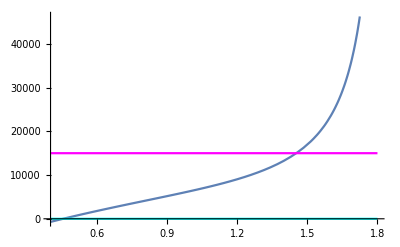

```mathematica
p1=Plot[(T /. Jämnvikt), {θ, 0.4, 1.8}];
p2 = Plot[15000,{θ, 0.4, 1.8},PlotStyle->Magenta];
p3 = Plot[0,{θ, 0.4, 1.8},PlotStyle->Hue[0.5]];
Show[p1,p2,p3]
```

#### F) Vad blir det maximala värdet för θ om vi inte behöver beakta linans begränsningar ? Lösning och svar med Mathematica kod

```mathematica
VectorAngle[d,OA]
UnitConvert[Quantity[1.849095985800008, "Radians"], "AngularDegrees"]
```

1.8491

105.945 °

## Problem 3 Ett experiment i en accelerator producerar ett grundämne som enbart finns i form av tre kortlivade isotoper. Dessa har halveringstider 2, 7 respektive 24 minuter. Den totala mängden/massan av ämnet, M, registreras sedan under någon tid efter experimentet. Se tabellen nedan.

## A) Ett experiment i en accelerator producerar ett grunda ämne som enbart finns i form av tre kortlivade isotoper.Dessa har halveringstider 2, 7 respektive 24 minuter.Den totala mängden/massan av ämnet, M, registreras sedan under någon tid efter experimentet. Se tabellen nedan. T1 = 2 minuter. T2 = 7 minuter. T3 = 24 minuter. λ = ln (2)/T M = M0* e^(-λ*t) 1 | 12.57 2 | 10.22 3 | 8.42 4 | 6.92 5 | 5.96 6 | 5.09 7 | 4.53 8 | 4.01 9 | 3.62 10 | 3.28 Lösning och svar med Mathematica koden:

```mathematica
ClearAll["Global`*"];
T1=2; " Svar till ett 3a"
T2=7;
T3=24;
λ1 = Log[2]/ T1;
λ2 = Log[2]/ T2;
λ3 = Log[2]/ T3;
M01;
M02;
M03;
Y={{12.57},{10.22},{8.42},{6.92},{5.96},{5.09},{4.53},{4.01},{3.62},{3.28}};
t = 1;
While[t < 11,
A[t]= {{E^(-λ1*t),E^(-λ2*t) ,E^(-λ3*t)}}
;t++]
r=Array[A,11-1];

B=ArrayReshape[r,{10,3}];
X ={{MO1},{MO2},{M03}};

 
"B.X= Y";
"Transpose[B].B.X = Transpose[B].Y";
a = Transpose[B].B ;
Dimensions[a];
q=Inverse[a];

Dimensions[q];
" X = a^-1.Transpose[B].Y";
s=q.Transpose[B].Y
```

Svar till ett 3a

{{9.71816},{4.46921},{1.74116}}

### B) De framräknade värdena ovan ger en modell, Ma(t), för totala mängden som funktion av tiden. Gör en grafisk jämförelse av Ma(t) och M i intervallet 0 ≤ t ≤ 10. Lösning med Mathematica koden:

```mathematica
Remove["Global`*"];
```

{{1/(√2),1/2^(1/7),1/2^(1/24)},{1/2,1/2^(2/7),1/2^(1/12)},{1/(2 √2),1/2^(3/7),1/2^(1/8)},{1/4,1/2^(4/7),1/2^(1/4)},{1/(4 √2),1/2^(5/7),1/2^(5/24)},{1/8,1/2^(6/7),1/2^(1/4)},{1/(8 √2),1/2,1/2^(1/24)},{1/16,1/(2 2^(1/7)),1/2^(1/3)},{1/(16 √2),1/(2 2^(2/7)),1/2^(3/8)},{1/32,1/(2 2^(3/7)),1/2^(5/12)}}

{{12.57},{10.22},{8.42},{6.92},{5.92},{5.09},{4.53},{4.01},{3.62},{3.28}}

{{M1},{M2},{M3}}

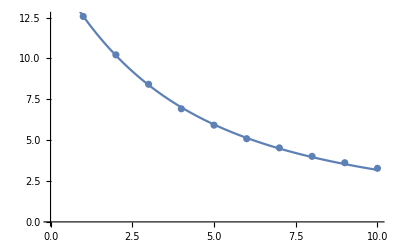

```mathematica
x={{2^(-1/2),2^(-1/7),2^(-1/24)},{2^(-1),2^(-2/7),2^(-1/12)},{2^(-3/2),2^(-3/7),2^(-1/8)},{2^(-2),2^(-4/7),2^(-1/4)},{2^(-5/2),2^(-5/7),2^(-5/24)},{2^(-3),2^(-6/7),2^(-1/4)},{2^(-7/2),2^(-1),2^(-1/24)},{2^(-4),2^(-8/7),2^(-1/3)},{2^(-9/2),2^(-9/7),2^(-9/24)},{2^(-5),2^(-10/7),2^(-10/24)}}
y={{12.57},{10.22},{8.42},{6.92},{5.92},{5.09},{4.53},{4.01},{3.62},{3.28}}
a={{M1},{M2},{M3}}
xt=Transpose[x];
newx=xt.x;
newy=xt.y;
innewX=Inverse[newx];
innewX.newy;
yandx={{1,12.57},{2,10.22},{3,8.42},{4,6.92},{5,5.92},{6,5.09},{7,4.53},{8,4.01},{9,3.62},{10,3.28}};
massa=ListPlot[yandx];
M=9.2048*2^(-t/2)+5.48483*2^(-t/7)+1.14228*2^(-t/24);
tid=Plot[M,{t ,0,10}];
Show[massa,tid]
```

### C) Antag i stället att två av isotoperna har samma halveringstid. Förklara varför det nu blir omöjligt att använda minsta kvadratmetoden om vi inte har ytterligare information om initiala förhållandet mellan mängderna av de två isotoper som har samma halveringstid. Svar: Om två isotoper har samma halveringstid så blir det ett överbestämt ekvationssystem och då saknar oftast systemet lösningar. Om det inte är tillrättalagt, vilket vi antar att det inte är då det rör sig om verkliga sönderfall.

Problem 4 
Vi vill modellera hur storleken på en fågel population varierar. För den aktuella arten/populationen antar vi att följande gäller:
1. Maximal livstid är 6 år.
2. Honorna blir fertila vid åldern 3 år.
3. Populationen är förhållandevis stor och livsvillkoren stabila över lång tid - vilket betyder att vi kan använda
tidsoberoende medelvärden för överlevnad och nativitet för olika årsklasser.

A)  Förklara varför n0(t) = f3n3(t) + f4n4(t) + f5n5(t) och n(k+1) (t + 1) = k = 0, 1, 2, 3, 4, där t ≥ 0
Svar: 
Hur många som föds till nästa tid period bestäm av hur många som finns i årsgruppen och hur stor nativiteten är för varje årsgrupp. Från uppgiften vet vi att det bara är från ålder 3-6 som fertila. Så det man måste
göra för att få redan på hur många som kommer att födas till nästa års kull är att multiplicera varje årsgrupps population med dess nativitet, sedan måste dessa adderas ihop så får man. 
 n0(t) = f3n3(t) + f4n4(t) + f5n5(t).
Hur många som kommer att leva i nästa generation N_k(t + 1) bestäm av att man tar som många som finns i N_k(t) och multiplicerar dem med det överlevands talet som finns  i tabeln, sedan måste  man bara göra så för varje årsgrupp.

### B) Formulera resultaten ovan som en 5 × 5 matris P verkande på en kolonnmatris (n1(t) n2(t)· · · n5(t))T. Visa att vi då får populationen vid tiden t + 1 uttryckt i populationen vid tiden t. Lösning och svar med Mathematica koden:

```mathematica
ClearAll["Global`*"]; 
P ={{0,0,S0*f3,S0*f4,S0*f5},{S1,0,0,0,0},{0,S2,0,0,0},{0,0,S3,0,0},{0,0,0,S4,0}} ;
 P1 ={{0,0,S0*f3,S0*f4,S0*f5},{S1,0,0,0,0},{0,S2,0,0,0},{0,0,S3,0,0},{0,0,0,S4,0}} // MatrixForm;
F ={{n1},{n2},{n3},{n4},{n5}} ;
F1 ={{n1},{n2},{n3},{n4},{n5}} //MatrixForm;

P1.F1
a= P.F
```

(0 | 0 | f3 S0 | f4 S0 | f5 S0
S1 | 0 | 0 | 0 | 0
0 | S2 | 0 | 0 | 0
0 | 0 | S3 | 0 | 0
0 | 0 | 0 | S4 | 0).(n1
n2
n3
n4
n5)

{{f3 n3 S0+f4 n4 S0+f5 n5 S0},{n1 S1},{n2 S2},{n3 S3},{n4 S4}}

### C) Antag följande värden: f3 = 3, f4 = 4, f5 = 3, s0 =12, s1 =35, s2 =12, s3 =12, s4 =25, samt ursprunglig population (n1(0)· · · n5(0))^T = 103(5 2 2 1 1)^T. Bestäm populationen vid tiden t = 30 (år). Går det att se en tendens ? Svar från Mathematica: 2647 fåglar kommer att dö ut. Lösning med Mathematica koden

{30.,2647.03}

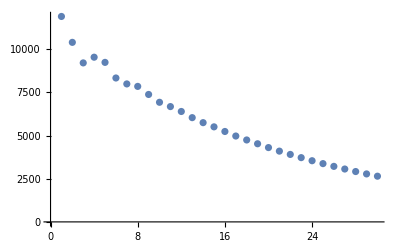

```mathematica
ClearAll["Global`*"];

S0 = 1/2;
S1= 3/5;
S2 = 1/2;
S3 = 1/2;
S4 = 2/5;
f3 = 3;
f4 = 4;
f5= 3;

n1 = 5 * 10^3;
n2 = 2*10^3;
n3 = 2*10^3;
n4  = 1*10^3;
n5 = 1 *10^3;

 P ={{0,0,S0*f3,S0*f4,S0*f5},{S1,0,0,0,0},{0,S2,0,0,0},{0,0,S3,0,0},{0,0,0,S4,0}} ;
F ={{n1},{n2},{n3},{n4},{n5}} ;

  k = 1;
While[k<31,
n00 = f3 n3 S0+f4 n4 S0+f5 n5 S0;
n11 = n1 S1;
n22 = n2 S2;
n33 = n3 S3;
n44 = n4 S4;
n1 = n00;
n2 = n11;
n3 = n22;
n4 = n33;
n5 = n44;
tot[k]= {k,n1+n2+n3+n4+n5};


 k ++]

w = Array[tot,30];
N[tot[30]]
ListPlot[w]
```

### D) Visa att populationen till slut kommer att dö ut. Lösning och svar med Mathematica koden

tot[1000.]

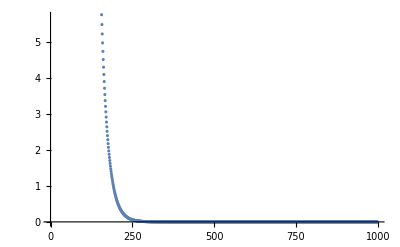

```mathematica
ClearAll["Global`*"];

S0 = 1/2;
S1= 3/5;
S2 = 1/2;
S3 = 1/2;
S4 = 2/5;
f3 = 3;
f4 = 4;
f5= 3;

n1 = 5 * 10^3;
n2 = 2*10^3;
n3 = 2*10^3;
n4  = 1*10^3;
n5 = 1 *10^3;

 P ={{0,0,S0*f3,S0*f4,S0*f5},{S1,0,0,0,0},{0,S2,0,0,0},{0,0,S3,0,0},{0,0,0,S4,0}} ;
F ={{n1},{n2},{n3},{n4},{n5}} ;

  k = 1;
While[k<1000,

n00 = f3 n3 S0+f4 n4 S0+f5 n5 S0;
n11 = n1 S1;
n22 = n2 S2;
n33 = n3 S3;
n44 = n4 S4;
n1 = n00;
n2 = n11;
n3 = n22;
n4 = n33;
n5 = n44;
tot[k]= {k,n1+n2+n3+n4+n5};


 k ++]

w = Array[tot,1000];
N[tot[1000]]
ListPlot[w]
```

### E) Antag att det är praktiskt genomförbart att lyfta överlevnadsandelen för årsklass 0 med t.ex. riktad foderutsättning. Vad måste s0 ändras till för att få en stabil population ? Ledning: Stabilitet kräver att ett av matrisens egenvärden Y k(där y är lamda)= 1. (Varför ?) Lösning och svar med Mathematica koden För att Om egen värdet är mindre än ett så kommer vektorn ( Som går från tidsaxeln till mängden population ) så kommer den nya vektorn som bildas när man multiplicerad med matrisen att bli mindre än den var innan men den kommer att behålla samma riktning.

```mathematica
ClearAll["Global`*"];

S1= 3/5;
S2 = 1/2;
S3 = 1/2;
S4 = 2/5;
f3 = 3;
f4 = 4;
f5= 3;

n1 = 5 * 10^3;
n2 = 2*10^3;
n3 = 2*10^3;
n4  = 1*10^3;
n5 = 1 *10^3;

 P ={{0,0,S0*f3,S0*f4,S0*f5},{S1,0,0,0,0},{0,S2,0,0,0},{0,0,S3,0,0},{0,0,0,S4,0}} ;
F ={{n1},{n2},{n3},{n4},{n5}} ;
Q = {{-λ,0,0,0,0},{0,-λ,0,0,0},{0,0,-λ,0,0},{0,0,0,-λ,0},{0,0,0,0,-λ}};
A = P+Q ;
λ = 1;
Solve[Det[A]==0,S0]
```

{{S0→25/42}}

### F) Välj det nya värdet för s0 från deluppgiften ovan och antag att vi startar med samma ursprungliga populationen som ovan. Vad blir totala antalet honor efter lång tid (inkluderad åldersklass 0) ? Lösning med Mathematica koden SVAR : den totala honor efter lång tid blir : 21097.7 honor (inkluderad med åldersklass 0)

21097.7

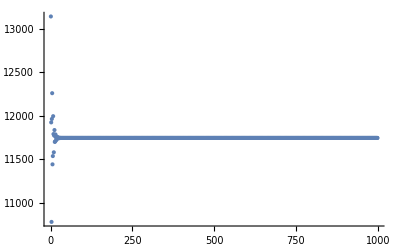

```mathematica
ClearAll["Global`*"];

S0 = 25/42;
S1= 3/5;
S2 = 1/2;
S3 = 1/2;
S4 = 2/5;
f3 = 3;
f4 = 4;
f5= 3;

n1 = 5 * 10^3;
n2 = 2*10^3;
n3 = 2*10^3;
n4  = 1*10^3;
n5 = 1 *10^3;

 P ={{0,0,S0*f3,S0*f4,S0*f5},{S1,0,0,0,0},{0,S2,0,0,0},{0,0,S3,0,0},{0,0,0,S4,0}} ;
F ={{n1},{n2},{n3},{n4},{n5}} ;

  k = 1;
While[k<1000,

n00 = f3 n3 S0+f4 n4 S0+f5 n5 S0;
n11 = n1 S1;
n22 = n2 S2;
n33 = n3 S3;
n44 = n4 S4;
n1 = n00;
n2 = n11;
n3 = n22;
n4 = n33;
n5 = n44;
tot[k]= {k,n1+n2+n3+n4+n5};



k ++]
 
tott= n1+n2+n3+n4+n5+f3*n3 + f4*n4 + f5*n5;
N[tott]
w = Array[tot,1000];
ListPlot[w]
```

## Referenser: * Grunnar Sparr / Linjär Algebra